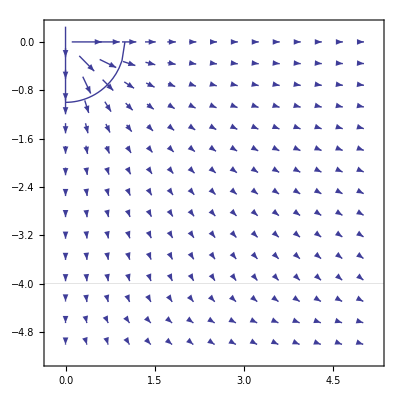

```mathematica
(*{{{x1,y1},{v1,v2}},...,{{xN,yN},{vN,vN}}}*)
Clear[mesh,meshpoints, plot,height]
mesh[xstep_,zstep_,numxsteps_,numzsteps_,h_,ϵ1_,ϵ2_,λ_]:=

Module[{},

generate [x_,z_]:=
If[x≠0∨z≠0,
If[z<=h,
{{x,-z},{ (λ x)/(2ϵ1 N[Pi](x^2+z^2)),-(λ z)/(2ϵ1 N[Pi](x^2+z^2)) }},
{{x,-z},{ (λ x)/(2ϵ1 N[Pi](x^2+z^2)),-(λ z)/(2ϵ2 N[Pi](x^2+z^2)) }}
]
];

(*what is the field at z=h? ie what direction should the = point ≤ or ≥ *)

t= Table[
(*x, z, |Subscript[E, ij]|, n - the normal vector *)
generate[i*xstep,j*zstep],
{j,0,numzsteps},
{i,0,numxsteps}
];
t = Flatten[t,1];
t = Delete[t,1]

]
height =4;
meshpoints = mesh[.5,.5,10,10,height,1,3,100];
radius = 1;
circle  = Table[{x,-Sqrt[radius^2-x^2]},{x,0,2,.05}];
plotC = ListLinePlot[circle];
plot = ListVectorPlot[meshpoints,GridLines-> {{},{-height}}];
Show[plot,plotC]
```

```mathematica
(*Optimized for field at boundary*)

xstep =.1;
numxsteps=100;
h=4;
λ=100;
ϵ1=1;
t= Table[
(*x, z, |Subscript[E, ij]|, n - the normal vector *)
{{i*xstep,-h},{ (λ i*xstep)/(2ϵ1 N[Pi]((i*xstep)^2+h^2)),-(λ h)/(2ϵ1 N[Pi]((i*xstep)^2+h^2)) }},
{i,0,numxsteps}
]
```

{{{0.,-4},{0.,-3.97887}},{{0.1,-4},{0.0994097,-3.97639}},{{0.2,-4},{0.198448,-3.96895}},{{0.3,-4},{0.296746,-3.95662}},{{0.4,-4},{0.393948,-3.93948}},{{0.5,-4},{0.489708,-3.91766}},{{0.6,-4},{0.583698,-3.89132}},{{0.7,-4},{0.675612,-3.86064}},{{0.8,-4},{0.765168,-3.82584}},{{0.9,-4},{0.852109,-3.78715}},{{1.,-4},{0.936206,-3.74482}},{{1.1,-4},{1.01726,-3.69913}},{{1.2,-4},{1.0951,-3.65034}},{{1.3,-4},{1.1696,-3.59876}},{{1.4,-4},{1.24063,-3.54465}},{{1.5,-4},{1.30812,-3.48833}},{{1.6,-4},{1.37203,-3.43006}},{{1.7,-4},{1.43231,-3.37014}},{{1.8,-4},{1.48898,-3.30883}},{{1.9,-4},{1.54204,-3.2464}},{{2.,-4},{1.59155,-3.1831}},{{2.1,-4},{1.63756,-3.11916}},{{2.2,-4},{1.68014,-3.0548}},{{2.3,-4},{1.71938,-2.99023}},{{2.4,-4},{1.75539,-2.92564}},{{2.5,-4},{1.78826,-2.86121}},{{2.6,-4},{1.81811,-2.7971}},{{2.7,-4},{1.84508,-2.73345}},{{2.8,-4},{1.86927,-2.67038}},{{2.9,-4},{1.89082,-2.60803}},{{3.,-4},{1.90986,-2.54648}},{{3.1,-4},{1.92651,-2.48582}},{{3.2,-4},{1.94091,-2.42614}},{{3.3,-4},{1.95318,-2.3675}},{{3.4,-4},{1.96345,-2.30994}},{{3.5,-4},{1.97183,-2.25352}},{{3.6,-4},{1.97845,-2.19827}},{{3.7,-4},{1.98341,-2.14422}},{{3.8,-4},{1.98682,-2.09139}},{{3.9,-4},{1.9888,-2.03979}},{{4.,-4},{1.98944,-1.98944}},{{4.1,-4},{1.98883,-1.94032}},{{4.2,-4},{1.98707,-1.89245}},{{4.3,-4},{1.98425,-1.84581}},{{4.4,-4},{1.98043,-1.8004}},{{4.5,-4},{1.97572,-1.75619}},{{4.6,-4},{1.97016,-1.71319}},{{4.7,-4},{1.96384,-1.67136}},{{4.8,-4},{1.95682,-1.63069}},{{4.9,-4},{1.94916,-1.59115}},{{5.,-4},{1.94091,-1.55273}},{{5.1,-4},{1.93214,-1.5154}},{{5.2,-4},{1.92288,-1.47914}},{{5.3,-4},{1.91318,-1.44391}},{{5.4,-4},{1.90309,-1.4097}},{{5.5,-4},{1.89265,-1.37648}},{{5.6,-4},{1.8819,-1.34421}},{{5.7,-4},{1.87087,-1.31289}},{{5.8,-4},{1.85959,-1.28247}},{{5.9,-4},{1.84809,-1.25294}},{{6.,-4},{1.8364,-1.22427}},{{6.1,-4},{1.82455,-1.19643}},{{6.2,-4},{1.81257,-1.1694}},{{6.3,-4},{1.80046,-1.14315}},{{6.4,-4},{1.78826,-1.11766}},{{6.5,-4},{1.77598,-1.09291}},{{6.6,-4},{1.76364,-1.06887}},{{6.7,-4},{1.75125,-1.04552}},{{6.8,-4},{1.73884,-1.02285}},{{6.9,-4},{1.72641,-1.00082}},{{7.,-4},{1.71398,-0.979415}},{{7.1,-4},{1.70155,-0.95862}},{{7.2,-4},{1.68914,-0.938414}},{{7.3,-4},{1.67677,-0.918776}},{{7.4,-4},{1.66442,-0.899689}},{{7.5,-4},{1.65213,-0.881135}},{{7.6,-4},{1.63988,-0.863096}},{{7.7,-4},{1.6277,-0.845557}},{{7.8,-4},{1.61558,-0.8285}},{{7.9,-4},{1.60353,-0.811911}},{{8.,-4},{1.59155,-0.795775}},{{8.1,-4},{1.57965,-0.780076}},{{8.2,-4},{1.56784,-0.7648}},{{8.3,-4},{1.55612,-0.749935}},{{8.4,-4},{1.54448,-0.735466}},{{8.5,-4},{1.53294,-0.721382}},{{8.6,-4},{1.52149,-0.70767}},{{8.7,-4},{1.51014,-0.694318}},{{8.8,-4},{1.49889,-0.681314}},{{8.9,-4},{1.48774,-0.668648}},{{9.,-4},{1.4767,-0.656309}},{{9.1,-4},{1.46575,-0.644287}},{{9.2,-4},{1.45491,-0.632571}},{{9.3,-4},{1.44418,-0.621153}},{{9.4,-4},{1.43355,-0.610023}},{{9.5,-4},{1.42303,-0.599172}},{{9.6,-4},{1.41262,-0.588591}},{{9.7,-4},{1.40231,-0.578272}},{{9.8,-4},{1.39211,-0.568208}},{{9.9,-4},{1.38201,-0.558389}},{{10.,-4},{1.37203,-0.54881}}}